```mathematica
setVariables[]

ΔE = 0;

ωE = 2*π*ϵ0;
ωB = 2*π*ϵ0;
Eamp[t_] := 0;
Bamp[t_] := 0;

Ubase = MatrixExp[-ⅈ*t*(HcorrectedStatic /. t->0)];

Zangle[U_] := zPhase[U[[2, 2]]/U[[1, 1]]]

δ0 = Hcorrected[[2, 2]] - Hcorrected[[1, 1]];

ΔE = 0;

Tmax = 1*10^-8;
U = ConjugateTranspose[Ubase].findEvolutionOperator[Hcorrected, Tmax];

Hcorrected // MatrixForm
(U /. t->Tmax) // MatrixForm

Zangle[U /. t->Tmax]
-2*π*(A/4)((d*e)/(h*Vt))*ΔE*Tmax

Hcorrected[[2, 2]] - Hcorrected[[1, 1]] - δ0
-2*π*(A/4)((d*e)/(h*Vt))*ΔE


clearVariables[]
```

(-340711. | 0. | 0. | 0 | 0. | 0. | 0 | 0
0. | -2.07034×10^8 | 0. | 0. | 0 | 0. | 0 | 0
0. | 0. | -2.39963×10^8 | 0. | 0 | -1.83967×10^8 | 0. | 0.
0 | 0. | 0. | -7.86089×10^7 | 0 | 0 | 0 | 0.
0. | 0 | 0 | 0 | 340711. | 0. | 0. | 0
0. | 0. | -1.83967×10^8 | 0 | 0. | -2.06239×10^8 | 0. | 0.
0 | 0 | 0. | 0 | 0. | 0. | -2.38801×10^8 | 0.
0 | 0 | 0. | 0. | 0 | 0. | 0. | -7.82948×10^7)

(1.-3.03577×10^-18 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 1.-1.43367×10^-10 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 1.+5.97867×10^-10 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | -2.14114×10^-11+5.46404×10^-10 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 1.-7.85993×10^-12 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 1.+1.73472×10^-18 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | -2.14116×10^-11+5.46403×10^-10 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 1.+4.97703×10^-10 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 1.-2.13739×10^-10 ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 1.-7.76657×10^-12 ⅈ)

-1.43367×10^-10

0.

0.

0.

```mathematica
D[δLab[2, 1], ΔE] /. ΔE->0
```

-(A d e π)/(2 √(h^2 Vt^2))

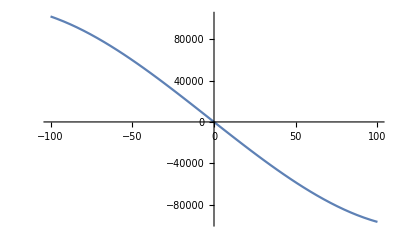

-2.40629×10^6

```mathematica
setVariables[]

ωE = 2*π*ϵ0;
ωB = 2*π*ϵ0;
Eamp[t_] := 0;
Bamp[t_] := 0;

Clear[ΔE]
Plot[(Hcorrected[[1, 1]] - Hcorrected[[2, 2]] /. ΔE->EE) - (Hcorrected[[1, 1]] - Hcorrected[[2, 2]] /. ΔE->0) + 2*π*(A/4)((d*e)/(h*Vt))*EE, {EE, -100, 100}]
(Hcorrected[[1, 1]] - Hcorrected[[2, 2]] /. ΔE->20) - (Hcorrected[[1, 1]] - Hcorrected[[2, 2]] /. ΔE->0)

clearVariables[]
```

```mathematica
δLab[2, 1] /. ΔE->0
```

1/2 π (A+4 B0 γn)